```mathematica
Needs["SciDraw`"]
```

SetDelayed::write: Tag MissingQ in MissingQ[expr_] is Protected.

𝒮𝒸𝒾𝒟𝓇𝒶𝓌: Publication–quality scientific figures with Mathematica
M. A. Caprio, University of Notre Dame
Version 0.0.7 (March 28, 2015)
View color paletteVisit home page  -Graphics-

## Import the data

```mathematica
data=Import["~/Downloads/Chicago_Traffic_Tracker_-_Historical_Congestion_Estimates_by_Region_-_2013-2018.csv","CSV"];
```

```mathematica
(*dateString[month_,day_,year_,hours_,minutes_,ampm_]:=Module[
{mon,d,h,m},

mon=If[month<10,"0"<>ToString[month],ToString[month]];
d=If[day<10,"0"<>ToString[day],ToString[day]];
h=If[hours<10,"0"<>ToString[hours],ToString[hours]];
m=If[minutes<10,"0"<>ToString[minutes],ToString[minutes]];

mon<>"/"<>d<>"/"<>ToString[year]<>" "<>h<>":"<>m<>" "<>ampm
]*)
```

### Clean data by year

```mathematica
data2018=Cases[data[[2;;All]],{date_,___}/;StringMatchQ[date,___~~"2018"~~___]];
```

```mathematica
data2017=Cases[data[[2;;All]],{date_,___}/;StringMatchQ[date,___~~"2017"~~___]];
```

```mathematica
data2016=Cases[data[[2;;All]],{date_,___}/;StringMatchQ[date,___~~"2016"~~___]];
```

```mathematica
data2015=Cases[data[[2;;All]],{date_,___}/;StringMatchQ[date,___~~"2015"~~___]];
```

```mathematica
data2014=Cases[data[[2;;All]],{date_,___}/;StringMatchQ[date,___~~"2014"~~___]];
```

```mathematica
data2013=Cases[data[[2;;All]],{date_,___}/;StringMatchQ[date,___~~"2013"~~___]];
```

```mathematica
data2018//Length
```

503266

```mathematica
data//Length
```

7089312

### Data header

```mathematica
data[[1]]//MatrixForm
```

(TIME
REGION_ID
BUS COUNT
NUMBER OF READS
SPEED)

### Finding the most congested regions using bus count

```mathematica
Table[Cases[data2018,{date_,region_,busCount_,reads_,speed_}/;region==n&&busCount>200]//Length,{n,1,29}]
```

{0,0,0,0,0,0,0,133,0,0,0,0,840,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[Cases[data2017,{date_,region_,busCount_,reads_,speed_}/;region==n&&busCount>200]//Length,{n,1,29}]
```

{0,0,0,0,0,0,0,256,0,0,0,0,2913,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[Cases[data2016,{date_,region_,busCount_,reads_,speed_}/;region==n&&busCount>200]//Length,{n,1,29}]
```

{0,0,0,0,0,0,0,296,0,0,0,0,3363,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[Cases[data2015,{date_,region_,busCount_,reads_,speed_}/;region==n&&busCount>200]//Length,{n,1,29}]
```

{0,0,0,0,0,0,0,194,0,0,0,0,1347,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[Cases[data2014,{date_,region_,busCount_,reads_,speed_}/;region==n&&busCount>200]//Length,{n,1,29}]
```

{0,0,0,0,0,0,0,165,0,0,0,0,2811,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[Cases[data2013,{date_,region_,busCount_,reads_,speed_}/;region==n&&busCount>200]//Length,{n,1,29}]
```

{0,0,0,0,0,0,0,139,0,0,0,0,2480,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Analyzing the data for region 8

```mathematica
DayName[{2018,02,05}]
```

Monday

Analyze April 2018

```mathematica
dateCumulative[day_,month_]:=Module[
{d,m,dateString,occurances},

d=If[day<10,"0"<>ToString[day],ToString[day]];
m=If[month<10,"0"<>ToString[month],ToString[month]];

dateString=StringJoin[m,"/",d,"/","2018"];

occurances=Cases[data2018,{date_,___,speed_}/;(StringContainsQ[date,dateString~~___])&&speed<15&&speed≠0]//Length;

Return[occurances]
]
```

```mathematica
Table[dateCumulative[n,4],{n,2,8}]
```

{63,113,89,87,85,25,0}

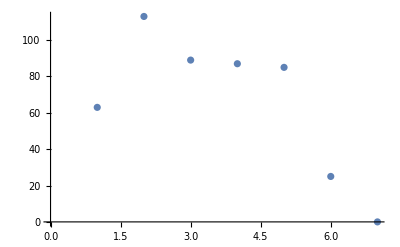

```mathematica
ListPlot[Table[dateCumulative[n,4],{n,2,8}]]
```

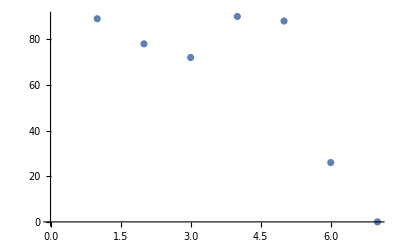

```mathematica
ListPlot[Table[dateCumulative[n,4],{n,9,15}]]
```

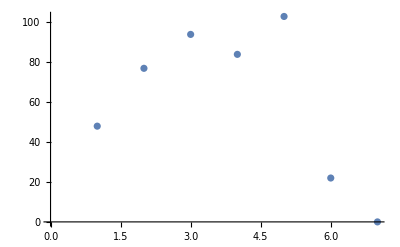

```mathematica
ListPlot[Table[dateCumulative[n,4],{n,16,22}]]
```

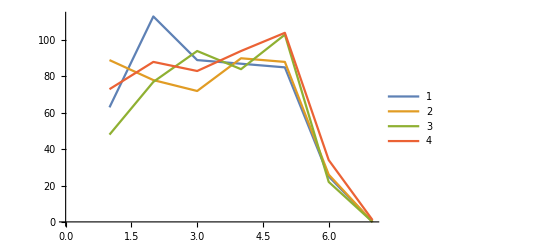

```mathematica
ListPlot[{Table[dateCumulative[n,4],{n,2,8}],Table[dateCumulative[n,4],{n,9,15}],Table[dateCumulative[n,4],{n,16,22}],Table[dateCumulative[n,4],{n,23,29}]},Joined->True,PlotLegends->{1,2,3,4}]
```

```mathematica
monthCumulative[month_,year_]:=Module[
{m,occurances},


m=If[month<10,"0"<>ToString[month],ToString[month]];

m=StringJoin[m,"/"];

occurances=Cases[data2017,{date_,___,speed_}/;(StringContainsQ[date,m~~___~~"/"~~ToString[year]~~___])&&speed<15&&speed≠0]//Length;

Return[occurances]
]
```

```mathematica
monthCumulative[04,2017]
```

1898

```mathematica
Cases[data2017,{date_,___,speed_}/;(StringContainsQ[date,"04/"~~___~~"/2017"~~___])&&speed<15&&speed≠0]//Length
```

1898

```mathematica
perMonth2017Data=Table[{n,monthCumulative[n,2017]},{n,1,12}]
```

{{1,1623},{2,1647},{3,2104},{4,1898},{5,2346},{6,2619},{7,2401},{8,2364},{9,1877},{10,2287},{11,2137},{12,1845}}

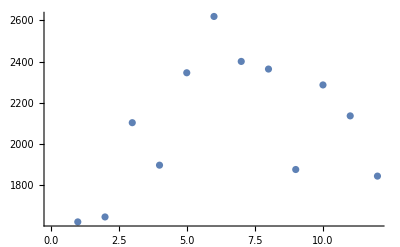

```mathematica
ListPlot[perMonth2017Data,Joined->False]
```

```mathematica
model1=a Exp[-(x-mu)^2/(2 sig^2)]
```

a ⅇ^(-(-mu+x)^2/(2 sig^2))

```mathematica
fit=FindFit[perMonth2017Data,model1,{{a,2500},{mu,5},{sig,4}},x]
```

{a→2380.12,mu→7.14639,sig→6.76177}

```mathematica
model1f=Function[{x},Evaluate[model1/.fit]]
```

Function[{x},2380.12 ⅇ^(-0.0109358 (-7.14639+x)^2)]

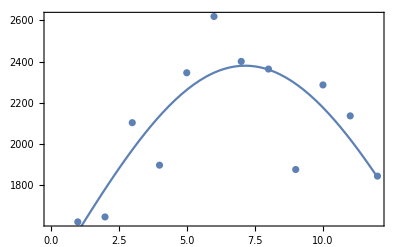

```mathematica
Show[ListPlot[perMonth2017Data],Plot[model1f[x],{x,1,12}],Frame->True]
```

```mathematica
Figure[
{
FigurePanel[
{

DataPlot[["plot"]][
perMonth2017Data,
DataLine->{LineColor->Firebrick}
];

FigLine[Plot[model1f[x],{x,1,12.5}]];

},
XPlotRange->{1,12},
YPlotRange->{1500,2650},
XExtendRange->0.1,
YExtendRange->0.01,
XFrameLabel->Row[{"Month"}],
YFrameLabel->Row[{"Congestion"}]
];

},
CanvasSize->{4.2,3.6}(*,
Export->True,
ExportFileName->filename,
ExportFormat->"PDF"*)
]
```

-Graphics-

```mathematica
week1=Table[{n-1,dateCumulative[n,4]},{n,2,8}]
```

{{1,63},{2,113},{3,89},{4,87},{5,85},{6,25},{7,0}}

```mathematica
week2=Table[{n-8,dateCumulative[n,4]},{n,9,15}]
```

{{1,89},{2,78},{3,72},{4,90},{5,88},{6,26},{7,0}}

```mathematica
week3=Table[{n-15,dateCumulative[n,4]},{n,16,22}]
```

{{1,48},{2,77},{3,94},{4,84},{5,103},{6,22},{7,0}}

```mathematica
week4=Table[{n-22,dateCumulative[n,4]},{n,23,29}]
```

{{1,73},{2,88},{3,83},{4,94},{5,104},{6,34},{7,1}}

```mathematica
Figure[
{
FigurePanel[
{
DataPlot[["week1"]][week1,DataLine->{LineColor->Firebrick},RightLabel->"Week1",TextOffset->{3,-6},TextColor->Firebrick];

DataPlot[week2,DataLine->{LineColor->Green},LeftLabel->"Week2",TextOffset->{3,6},TextColor->Green];

DataPlot[week3,DataLine->{LineColor->Blue},TailLabel->"Week3",TextOffset->{-1,2},TextColor->Blue];

DataPlot[week4,DataLine->{LineColor->Brown},CenterLabel->"Week4",
TextOffset->{-1,-2},TextColor->Brown];

FigLabel[{2,1.5},"April 2018",FontSize->20];

},
XPlotRange->{1,7},
YPlotRange->{0,125},
XExtendRange->{0.10,0.05},
YExtendRange->{0.1,0},
XFrameLabel->Row[{"Day"}],
YFrameLabel->Row[{"Congestion"}]
];

},
CanvasSize->{4.2,3.6}(*,
Export->True,
ExportFileName->filename,
ExportFormat->"PDF"*)
]
```

-Graphics-

```mathematica
Options[DataPlot]
```

{CenterFontFamily→Default,CenterFontSize→Default,CenterFontSlant→Default,CenterFontTracking→Default,CenterFontVariations→Default,CenterFontWeight→Default,CenterLabel→None,CenterLabelPosition→Automatic,CenterShowText→Default,CenterTextBackground→Default,CenterTextBaseBuffer→Default,CenterTextBuffer→Default,CenterTextCallout→Default,CenterTextCalloutCapForm→Default,CenterTextCalloutColor→Default,CenterTextCalloutDashing→Default,CenterTextCalloutDirectives→Default,CenterTextCalloutJoinForm→Default,CenterTextCalloutOpacity→Default,CenterTextCalloutThickness→Default,CenterTextColor→Default,CenterTextFrame→Default,CenterTextFrameColor→Default,CenterTextMargin→Default,CenterTextNudge→Default,CenterTextOffset→Default,CenterTextOpacity→Default,CenterTextOrientation→Default,CenterTextPadding→Default,CenterTextRectify→Default,CenterTextRoundingRadius→Default,CenterTextStyleOptions→Default,Color→Inherited,ColumnNames→None,DataColumns→{1,2},DataDrop→{},DataFill→{},DataFilters→None,DataLine→{},DataSymbol→{},Debug→Inherited,Directives→Inherited,Epilog→Inherited,FillColor→Inherited,FillDirectives→Inherited,FillOpacity→Inherited,FontFamily→Inherited,FontSize→Inherited,FontSlant→Inherited,FontTracking→Inherited,FontVariations→Inherited,FontWeight→Inherited,HeadFontFamily→Default,HeadFontSize→Default,HeadFontSlant→Default,HeadFontTracking→Default,HeadFontVariations→Default,HeadFontWeight→Default,HeadLabel→None,HeadLabelPosition→Automatic,HeadShowText→Default,HeadTextBackground→Default,HeadTextBaseBuffer→Default,HeadTextBuffer→Default,HeadTextCallout→Default,HeadTextCalloutCapForm→Default,HeadTextCalloutColor→Default,HeadTextCalloutDashing→Default,HeadTextCalloutDirectives→Default,HeadTextCalloutJoinForm→Default,HeadTextCalloutOpacity→Default,HeadTextCalloutThickness→Default,HeadTextColor→Default,HeadTextFrame→Default,HeadTextFrameColor→Default,HeadTextMargin→Default,HeadTextNudge→Default,HeadTextOffset→Default,HeadTextOpacity→Default,HeadTextOrientation→Horizontal,HeadTextPadding→Default,HeadTextRectify→Default,HeadTextRoundingRadius→Default,HeadTextStyleOptions→Default,Layer→Inherited,LeftFontFamily→Default,LeftFontSize→Default,LeftFontSlant→Default,LeftFontTracking→Default,LeftFontVariations→Default,LeftFontWeight→Default,LeftLabel→None,LeftLabelPosition→Automatic,LeftShowText→Default,LeftTextBackground→Default,LeftTextBaseBuffer→Default,LeftTextBuffer→Default,LeftTextCallout→Default,LeftTextCalloutCapForm→Default,LeftTextCalloutColor→Default,LeftTextCalloutDashing→Default,LeftTextCalloutDirectives→Default,LeftTextCalloutJoinForm→Default,LeftTextCalloutOpacity→Default,LeftTextCalloutThickness→Default,LeftTextColor→Default,LeftTextFrame→Default,LeftTextFrameColor→Default,LeftTextMargin→Default,LeftTextNudge→Default,LeftTextOffset→Default,LeftTextOpacity→Default,LeftTextOrientation→Default,LeftTextPadding→Default,LeftTextRectify→Default,LeftTextRoundingRadius→Default,LeftTextStyleOptions→Default,LineCapForm→Inherited,LineColor→Inherited,LineDashing→Inherited,LineDirectives→Inherited,LineJoinForm→Inherited,LineOpacity→Inherited,LineThickness→Inherited,Opacity→Inherited,PointColor→Inherited,PointDirectives→Inherited,PointFontFamily→Default,PointFontSize→Default,PointFontSlant→Default,PointFontTracking→Default,PointFontVariations→Default,PointFontWeight→Default,PointLabel→None,PointLabelPosition→Automatic,PointOpacity→Inherited,PointShowText→Default,PointSize→Inherited,PointTextBackground→Default,PointTextBaseBuffer→Default,PointTextBuffer→Default,PointTextCallout→Default,PointTextCalloutCapForm→Default,PointTextCalloutColor→Default,PointTextCalloutDashing→Default,PointTextCalloutDirectives→Default,PointTextCalloutJoinForm→Default,PointTextCalloutOpacity→Default,PointTextCalloutThickness→Default,PointTextColor→Default,PointTextFrame→Default,PointTextFrameColor→Default,PointTextMargin→Default,PointTextNudge→Default,PointTextOffset→Default,PointTextOpacity→Default,PointTextOrientation→Default,PointTextPadding→Default,PointTextRectify→Default,PointTextRoundingRadius→Default,PointTextStyleOptions→Default,Print→False,Prolog→Inherited,RightFontFamily→Default,RightFontSize→Default,RightFontSlant→Default,RightFontTracking→Default,RightFontVariations→Default,RightFontWeight→Default,RightLabel→None,RightLabelPosition→Automatic,RightShowText→Default,RightTextBackground→Default,RightTextBaseBuffer→Default,RightTextBuffer→Default,RightTextCallout→Default,RightTextCalloutCapForm→Default,RightTextCalloutColor→Default,RightTextCalloutDashing→Default,RightTextCalloutDirectives→Default,RightTextCalloutJoinForm→Default,RightTextCalloutOpacity→Default,RightTextCalloutThickness→Default,RightTextColor→Default,RightTextFrame→Default,RightTextFrameColor→Default,RightTextMargin→Default,RightTextNudge→Default,RightTextOffset→Default,RightTextOpacity→Default,RightTextOrientation→Default,RightTextPadding→Default,RightTextRectify→Default,RightTextRoundingRadius→Default,RightTextStyleOptions→Default,Show→Inherited,ShowFill→Inherited,ShowLine→Inherited,ShowPoint→Inherited,ShowText→Inherited,Style→Inherited,SymbolOptionColumns→None,TailFontFamily→Default,TailFontSize→Default,TailFontSlant→Default,TailFontTracking→Default,TailFontVariations→Default,TailFontWeight→Default,TailLabel→None,TailLabelPosition→Automatic,TailShowText→Default,TailTextBackground→Default,TailTextBaseBuffer→Default,TailTextBuffer→Default,TailTextCallout→Default,TailTextCalloutCapForm→Default,TailTextCalloutColor→Default,TailTextCalloutDashing→Default,TailTextCalloutDirectives→Default,TailTextCalloutJoinForm→Default,TailTextCalloutOpacity→Default,TailTextCalloutThickness→Default,TailTextColor→Default,TailTextFrame→Default,TailTextFrameColor→Default,TailTextMargin→Default,TailTextNudge→Default,TailTextOffset→Default,TailTextOpacity→Default,TailTextOrientation→Horizontal,TailTextPadding→Default,TailTextRectify→Default,TailTextRoundingRadius→Default,TailTextStyleOptions→Default,TextBackground→Inherited,TextBaseBuffer→Inherited,TextBuffer→Inherited,TextCallout→Inherited,TextCalloutCapForm→Inherited,TextCalloutColor→Inherited,TextCalloutDashing→Inherited,TextCalloutDirectives→Inherited,TextCalloutJoinForm→Inherited,TextCalloutOpacity→Inherited,TextCalloutThickness→Inherited,TextColor→Inherited,TextFrame→Inherited,TextFrameColor→Inherited,TextMargin→Inherited,TextNudge→Inherited,TextOffset→Inherited,TextOpacity→Inherited,TextOrientation→Inherited,TextPadding→Inherited,TextRectify→Inherited,TextRoundingRadius→Inherited,TextStyleOptions→Inherited,XAxisScale→None,XErrorColumn→None,YAxisScale→None,YErrorColumn→None}